```mathematica
eded=Monitor[Table[Chromial[k],{k,1,300000}],k];Length[eded]
```

0

```mathematica
FromNormalToComplete[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS2[i-1,j-1]]],{i,1,length},{j,1,length}]
```

```mathematica
FromCompleteToNormal[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS1[i-1,j-1]]],{i,1,length},{j,1,length}]
```

```mathematica
MatrixForm[FromNormalToComplete[7]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 3 | 1 | 0 | 0 | 0 | 0
1 | 7 | 6 | 1 | 0 | 0 | 0
1 | 15 | 25 | 10 | 1 | 0 | 0
1 | 31 | 90 | 65 | 15 | 1 | 0
1 | 63 | 301 | 350 | 140 | 21 | 1)

```mathematica
Table[
With[{g=Chromial[k]},
With[
{a=CompleteBaseCoeff[g],b=CoefficientList[g,x]},

{a.FromCompleteToNormal[VertexCount[ReadGrof[k]]+1],b}
]
],
{k,1,10}]
```

{{{0,-6,11,-6,1},{0,-6,11,-6,1}},{{0,18,-39,29,-9,1},{0,18,-39,29,-9,1}},{{0,-54,135,-126,56,-12,1},{0,-54,135,-126,56,-12,1}},{{0,-64,154,-137,58,-12,1},{0,-64,154,-137,58,-12,1}},{{0,162,-459,513,-294,92,-15,1},{0,162,-459,513,-294,92,-15,1}},{{0,192,-526,565,-311,94,-15,1},{0,192,-526,565,-311,94,-15,1}},{{0,210,-565,594,-320,95,-15,1},{0,210,-565,594,-320,95,-15,1}},{{0,162,-459,513,-294,92,-15,1},{0,162,-459,513,-294,92,-15,1}},{{0,162,-459,513,-294,92,-15,1},{0,162,-459,513,-294,92,-15,1}},{{0,-486,1539,-1998,1395,-570,137,-18,1},{0,-486,1539,-1998,1395,-570,137,-18,1}}}

```mathematica
Table[MatrixForm[Inverse[FromCompleteToNormal[k]*FromNormalToCycle[k]]],{k,1,8}]
```

{(1),(1 | 0
0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 2 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 2 | 1 | 0
0 | 10 | 9 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0
0 | 10 | 9 | 1 | 0
0 | 156 | 150 | 24 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0
0 | 10 | 9 | 1 | 0 | 0
0 | 156 | 150 | 24 | 1 | 0
0 | 4916 | 4850 | 850 | 50 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0
0 | 10 | 9 | 1 | 0 | 0 | 0
0 | 156 | 150 | 24 | 1 | 0 | 0
0 | 4916 | 4850 | 850 | 50 | 1 | 0
0 | 284160 | 281640 | 50400 | 3225 | 90 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 10 | 9 | 1 | 0 | 0 | 0 | 0
0 | 156 | 150 | 24 | 1 | 0 | 0 | 0
0 | 4916 | 4850 | 850 | 50 | 1 | 0 | 0
0 | 284160 | 281640 | 50400 | 3225 | 90 | 1 | 0
0 | 27177928 | 26961564 | 4845610 | 316050 | 9555 | 147 | 1)}

```mathematica
Table[MatrixForm[Inverse[FromNormalToCycle[k]]* FromNormalToComplete[k]],{k,1,10}]
```

{(1),(1 | 0
0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | -2 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | -2 | 1 | 0
0 | 2 | -9 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0
0 | 2 | -9 | 1 | 0
0 | -4 | 42 | -24 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0 | 0
0 | 2 | -9 | 1 | 0 | 0
0 | -4 | 42 | -24 | 1 | 0
0 | 4 | -150 | 250 | -50 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0 | 0 | 0
0 | 2 | -9 | 1 | 0 | 0 | 0
0 | -4 | 42 | -24 | 1 | 0 | 0
0 | 4 | -150 | 250 | -50 | 1 | 0
0 | -6 | 465 | -1800 | 975 | -90 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 2 | -9 | 1 | 0 | 0 | 0 | 0
0 | -4 | 42 | -24 | 1 | 0 | 0 | 0
0 | 4 | -150 | 250 | -50 | 1 | 0 | 0
0 | -6 | 465 | -1800 | 975 | -90 | 1 | 0
0 | 6 | -1323 | 10535 | -12250 | 2940 | -147 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -9 | 1 | 0 | 0 | 0 | 0 | 0
0 | -4 | 42 | -24 | 1 | 0 | 0 | 0 | 0
0 | 4 | -150 | 250 | -50 | 1 | 0 | 0 | 0
0 | -6 | 465 | -1800 | 975 | -90 | 1 | 0 | 0
0 | 6 | -1323 | 10535 | -12250 | 2940 | -147 | 1 | 0
0 | -8 | 3556 | -54096 | 119070 | -58800 | 7448 | -224 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -9 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -4 | 42 | -24 | 1 | 0 | 0 | 0 | 0 | 0
0 | 4 | -150 | 250 | -50 | 1 | 0 | 0 | 0 | 0
0 | -6 | 465 | -1800 | 975 | -90 | 1 | 0 | 0 | 0
0 | 6 | -1323 | 10535 | -12250 | 2940 | -147 | 1 | 0 | 0
0 | -8 | 3556 | -54096 | 119070 | -58800 | 7448 | -224 | 1 | 0
0 | 8 | -9180 | 254100 | -979020 | 875826 | -222264 | 16632 | -324 | 1)}

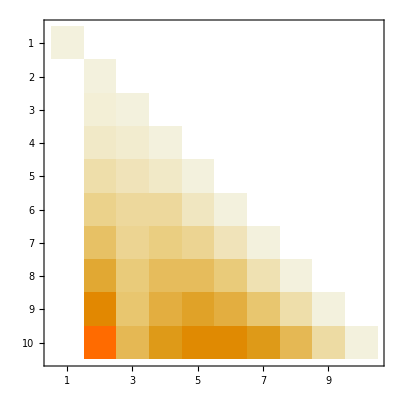
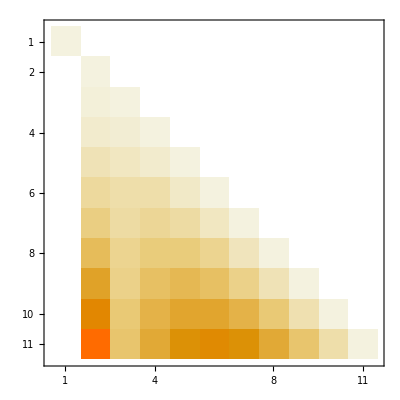
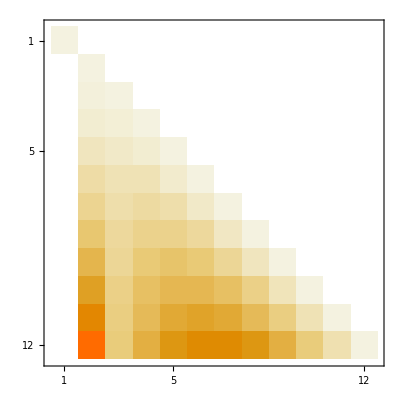
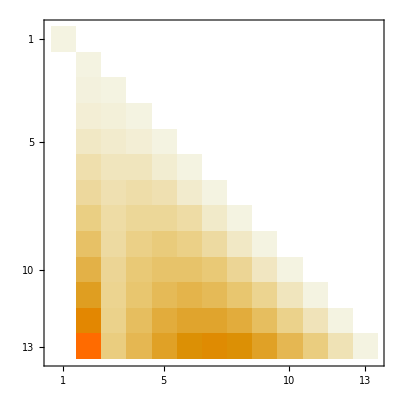
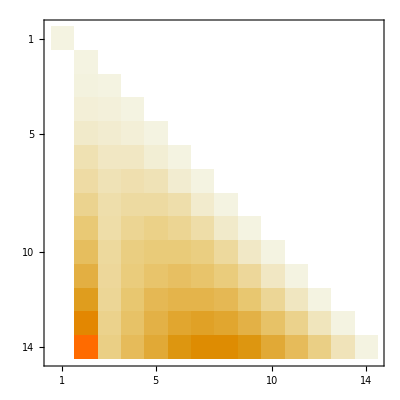
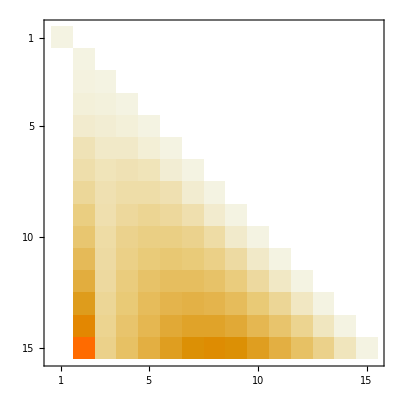
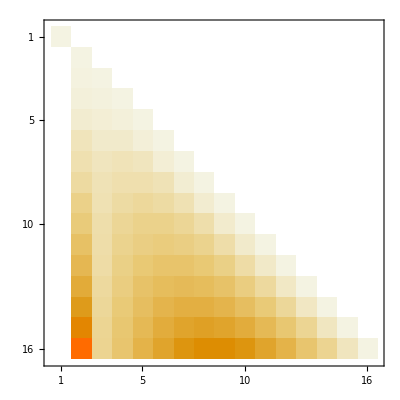
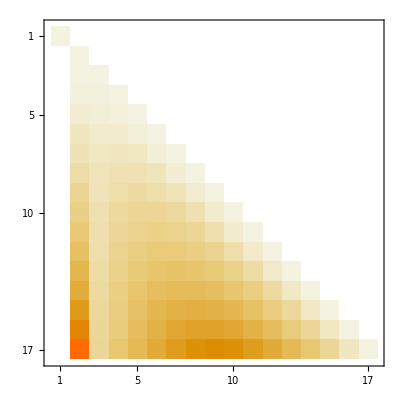

```mathematica
Table[MatrixPlot[FromNormalToCycle[k]],{k,10,20}]
```

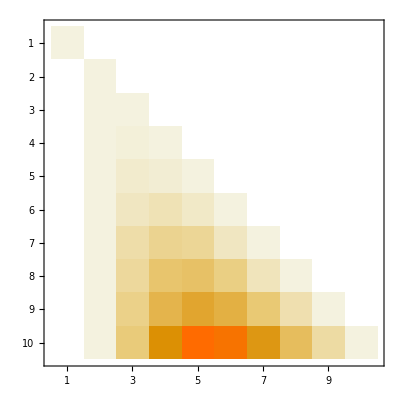
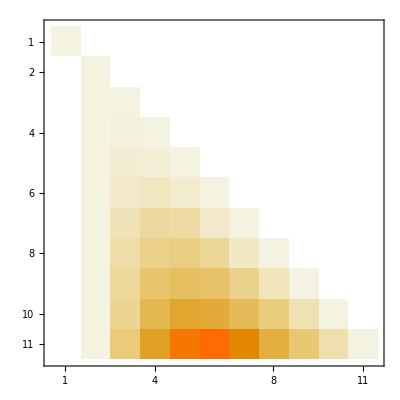
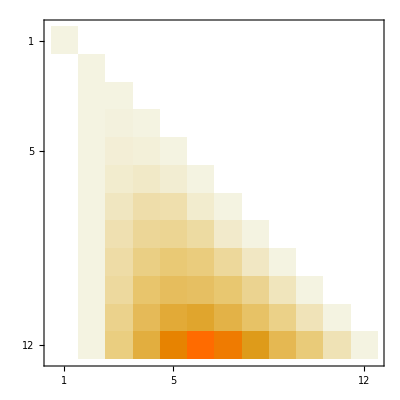
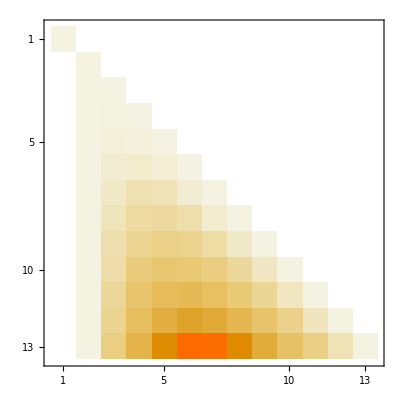
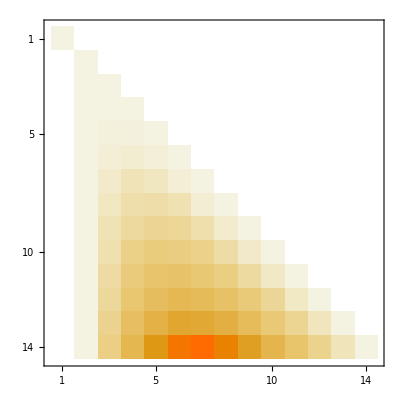
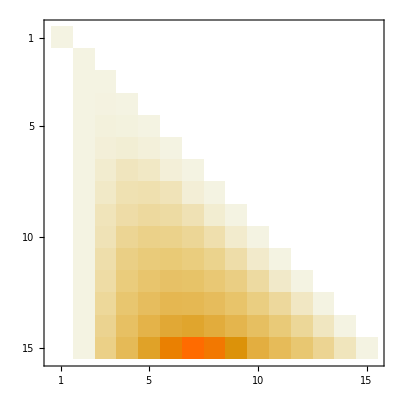
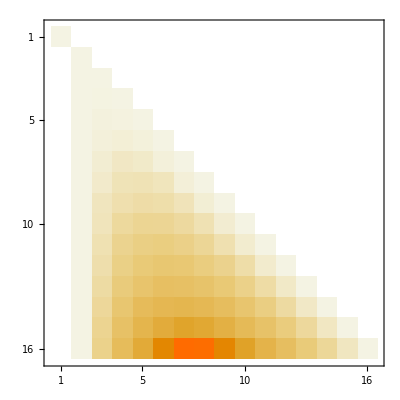
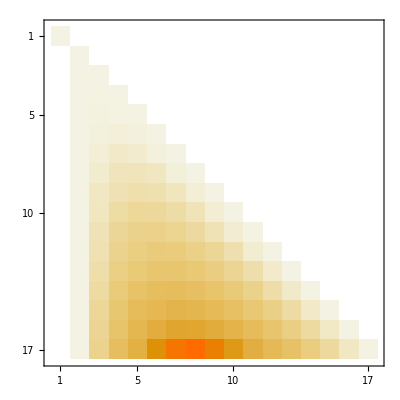

```mathematica
Table[MatrixPlot[FromNormalToComplete[k]],{k,10,20}]
```

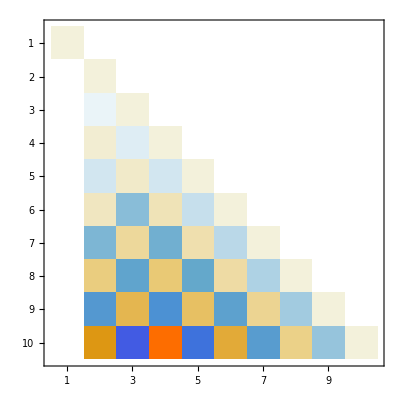
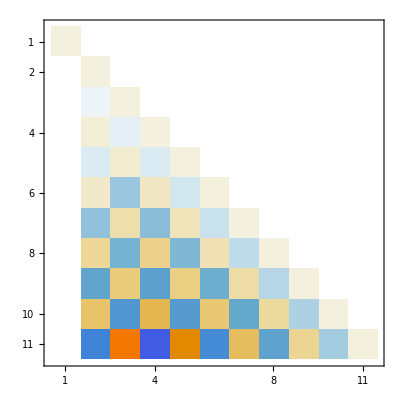
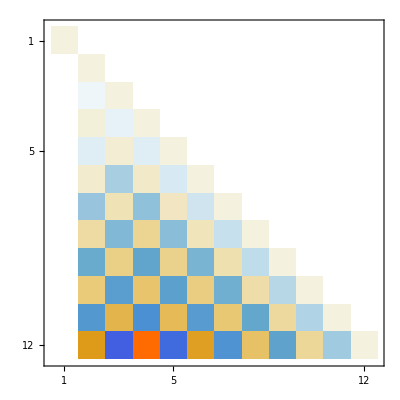
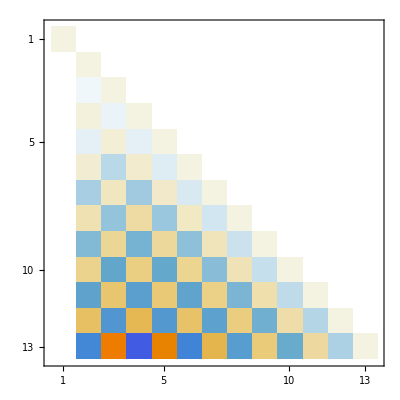
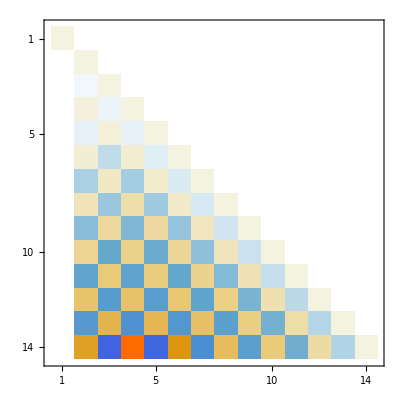
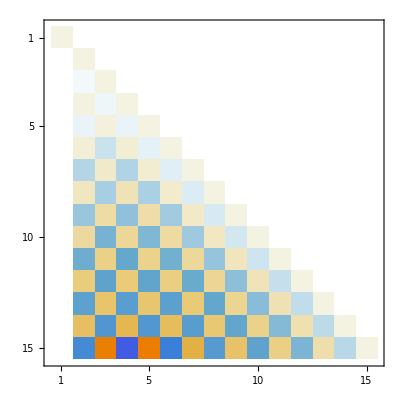
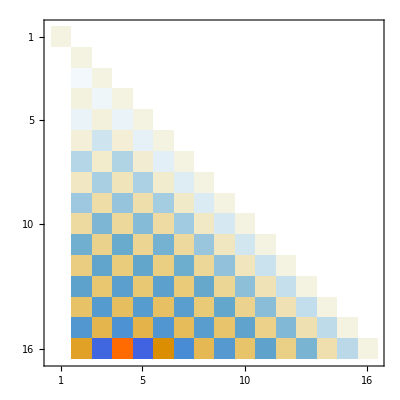
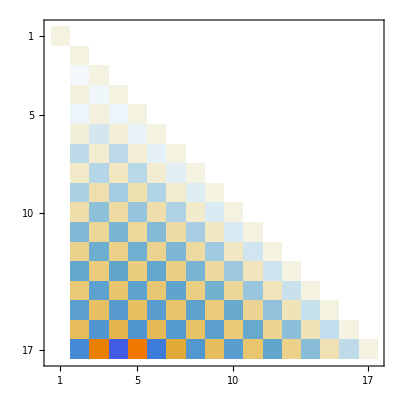

```mathematica
Table[MatrixPlot[FromCompleteToNormal[k]],{k,10,20}]
```

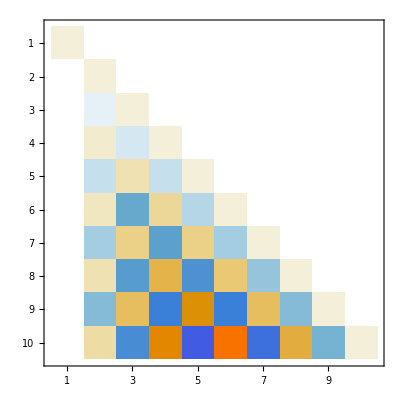
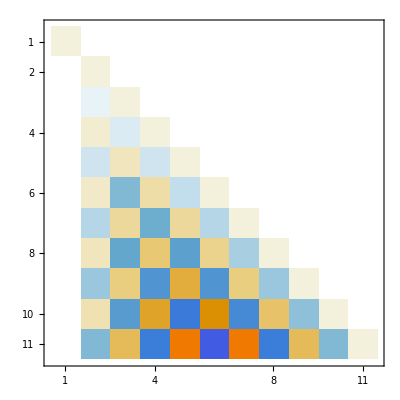
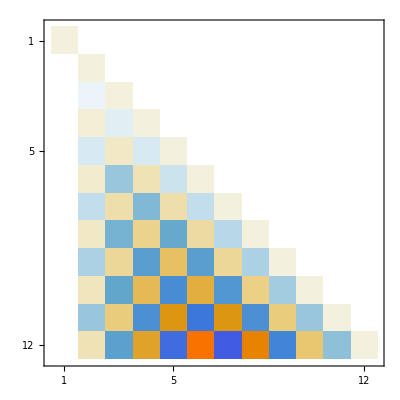
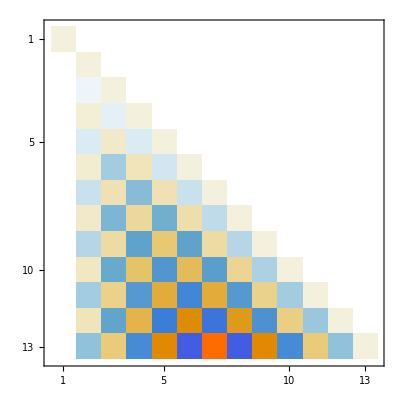
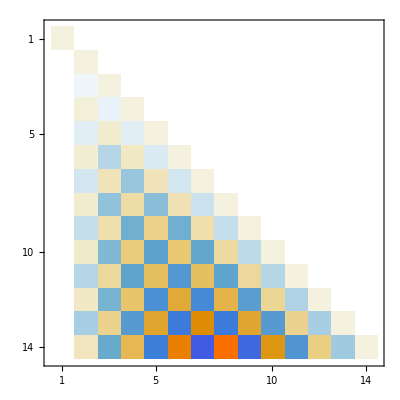
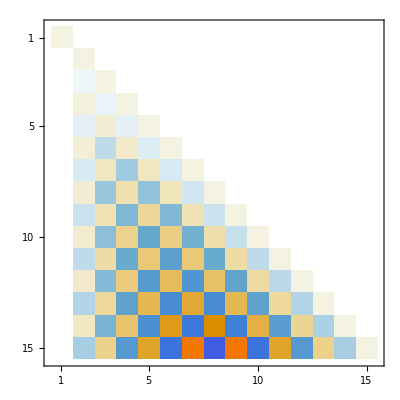
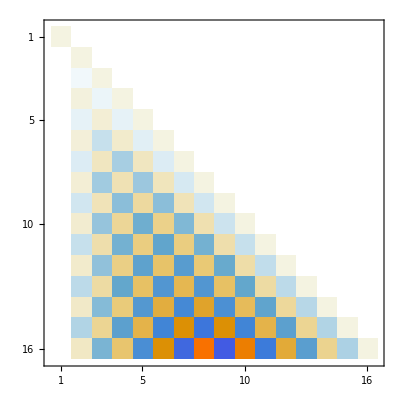
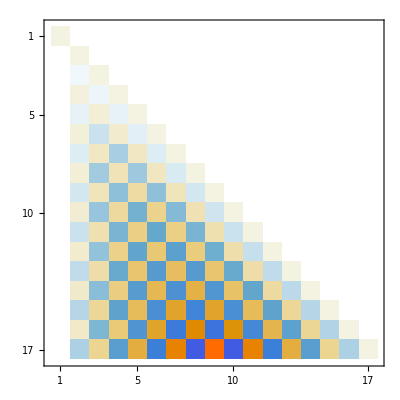

```mathematica
Table[MatrixPlot[Inverse[FromNormalToCycle[k]]],{k,10,20}]
```